# Serienschwingkreis

## Funktionen

### Includes

```mathematica
<<"Labor.m"
Needs["ErrorBarPlots`"]
Needs["ErrorBarLogPlots`"]
Gauss[a_]:= Module[{},{Mean[a],StandardDeviation[a]/Sqrt[Length[a]]}];
```

## Geräteliste

Oszi:
true rms:

## 1.) Resonanzfrequenz (Bestimmung aus Phasenverlauf am Widerstand)

### Induktivität und Kapazität

```mathematica
l={3,0}*10^-3;
rl=0.5;
c={0.15,0.01}*10^-6;
r={10,0};
```

### Theoretische Resonanzfrequenz

```mathematica
(Elec`Fω[l[[1]],l[[2]],c[[1]],c[[2]]])/(2*π)
```

{7502.64,250.088}

```mathematica
1/(2*π)*√(1/(l[[1]]*c[[1]])-rl^2/l[[1]]^2)
```

7502.59

### Theroretische Güte Q

```mathematica
Elec`FQ[r[[1]],r[[2]],l[[1]],l[[2]],c[[1]],c[[2]]]
```

{14.1421,0.471405}

```mathematica
Begin["R`"];
```

### Messung (Achtung! Konstante Eingangsspannung von 2 V Spitze-Spitze, manuell nachregeln!)

```mathematica
M={{"f/Hz", "Ua/V", "δt", "Ue/V"}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}}; dM={{"Δf/Hz", "ΔUa/V", "Δδt", "ΔUe/V"}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}};

Ue=4;(*eff, fluke 175*)
due=0.4;
```

### Amplitudengang

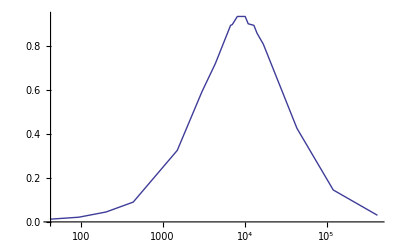

```mathematica
ListLogLinearPlot[Table[{M[[x,1]], M[[x,2]]/M[[x,4]]},{x,2,Length[M]}],Joined -> True]
```

```mathematica
At=Table[Basic`Fdiv[M[[x,2]],dM[[x,2]],M[[x,4]],dM[[x,4]]],{x,2,Length[M]}];
p1 = Table[{{M[[x,1]],10 Log[At[[x-1,1]]]},ErrorBar[dM[[x,1]],At[[x-1,2]]]},{x,2,Length[M]}];
```

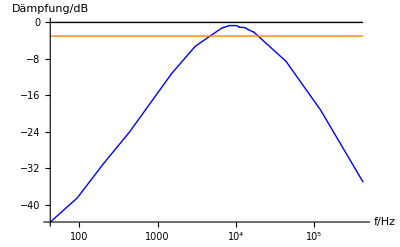

```mathematica
Show[ErrorListLogLinearPlot[p1,Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{-3},{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange,Black}],
(*ListLogLinearPlot[{{9233.33,10},{9233.33,-50}},Joined ->True,PlotStyle-> {Brown}],*)
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

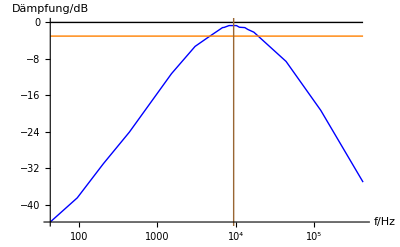

```mathematica
Show[ListLogLinearPlot[Table[{M[[x,1]],10 Log[M[[x,2]]/M[[x,4]]]},{x,2,Length[M]}],Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{-3},{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange,Black}],
ListLogLinearPlot[{{9360,10},{9360,-50}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

### Phasengang

```mathematica
ϕ=Table[Basic`Fmult[M[[x,3]],dM[[x,3]],M[[x,1]],dM[[x,1]]]*360,{x,2,Length[M]}];
p2 = Table[{{M[[x,1]],ϕ[[x-1,1]]},ErrorBar[dM[[x,1]],ϕ[[x-1,2]]]},{x,2,Length[M]}];
```

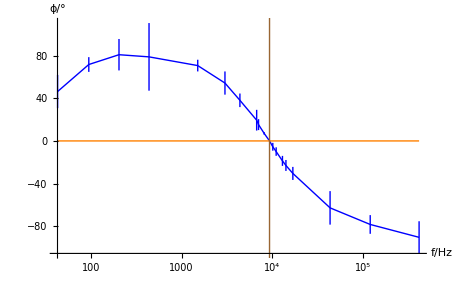

```mathematica
Show[ErrorListLogLinearPlot[p2,Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange}],
ListLogLinearPlot[{{9360,-120},{9360,120}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel-> {"f/Hz","ϕ/°"}]
```

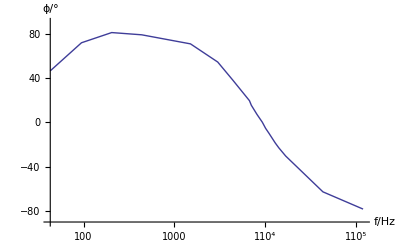

```mathematica
p3=Table[{M[[x,1]],M[[x,1]]*M[[x,3]]*360},{x,2,Length[M]-1}];
ListLogLinearPlot[p3,AxesLabel-> {"f/Hz","ϕ/°"},Joined-> True,PlotRange-> {{0,10^6},{-90,90}}]
```

## Amplitudengang und Phasengang der Induktivität

```mathematica
Begin["I`"];
```

### Messung (Achtung! Konstante Eingangsspannung von 2 V Spitze-Spitze, manuell nachregeln!)

```mathematica
M={{"f/Hz", "Ua/V", "δt", "Ue/V"}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}}; dM={{"Δf/Hz", "ΔUa/V", "Δδt", "ΔUe/V"}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}};

Ue=4;(*eff, fluke 175*)
due=0.4;
```

### Amplitudengang

```mathematica
ListLogLinearPlot[Table[{M[[x,1]], M[[x,2]]/M[[x,4]]},{x,2,Length[M]}],Joined -> True]
```

-Graphics-

```mathematica
At=Table[Basic`Fdiv[M[[x,2]],dM[[x,2]],M[[x,4]],dM[[x,4]]],{x,2,Length[M]}];
p1 = Table[{{M[[x,1]],10 Log[At[[x-1,1]]]},ErrorBar[dM[[x,1]],At[[x-1,2]]]},{x,2,Length[M]}];
```

```mathematica
Show[ErrorListLogLinearPlot[p1,Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{-3},{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange,Black}],
(*ListLogLinearPlot[{{9233.33,10},{9233.33,-50}},Joined ->True,PlotStyle-> {Brown}],*)
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

-Graphics-

```mathematica
Show[ListLogLinearPlot[Table[{M[[x,1]],10 Log[M[[x,2]]/M[[x,4]]]},{x,2,Length[M]}],Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{-3},{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange,Black}],
ListLogLinearPlot[{{9360,10},{9360,-50}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

-Graphics-

### Phasengang

```mathematica
ϕ=Table[Basic`Fmult[M[[x,3]],dM[[x,3]],M[[x,1]],dM[[x,1]]]*360,{x,2,Length[M]}];
p2 = Table[{{M[[x,1]],ϕ[[x-1,1]]},ErrorBar[dM[[x,1]],ϕ[[x-1,2]]]},{x,2,Length[M]}];
```

```mathematica
Show[ErrorListLogLinearPlot[p2,Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange}],
ListLogLinearPlot[{{9360,-120},{9360,120}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel-> {"f/Hz","ϕ/°"}]
```

-Graphics-

```mathematica
p3=Table[{M[[x,1]],M[[x,1]]*M[[x,3]]*360},{x,2,Length[M]-1}];
ListLogLinearPlot[p3,AxesLabel-> {"f/Hz","ϕ/°"},Joined-> True,PlotRange-> {{0,10^6},{-90,90}}]
```

-Graphics-

```mathematica
End[];
```

## Amplitudengang und Phasengang der Kapazität

```mathematica
Begin["C`"];
```

### Messung (Achtung! Konstante Eingangsspannung von 2 V Spitze-Spitze, manuell nachregeln!)

```mathematica
M={{"f/Hz", "Ua/V", "δt", "Ue/V"}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}}; dM={{"Δf/Hz", "ΔUa/V", "Δδt", "ΔUe/V"}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}};

Ue=4;(*eff, fluke 175*)
due=0.4;
```

### Amplitudengang

```mathematica
ListLogLinearPlot[Table[{M[[x,1]], M[[x,2]]/M[[x,4]]},{x,2,Length[M]}],Joined -> True]
```

-Graphics-

```mathematica
At=Table[Basic`Fdiv[M[[x,2]],dM[[x,2]],M[[x,4]],dM[[x,4]]],{x,2,Length[M]}];
p1 = Table[{{M[[x,1]],10 Log[At[[x-1,1]]]},ErrorBar[dM[[x,1]],At[[x-1,2]]]},{x,2,Length[M]}];
```

```mathematica
Show[ErrorListLogLinearPlot[p1,Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{-3},{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange,Black}],
(*ListLogLinearPlot[{{9233.33,10},{9233.33,-50}},Joined ->True,PlotStyle-> {Brown}],*)
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

-Graphics-

```mathematica
Show[ListLogLinearPlot[Table[{M[[x,1]],10 Log[M[[x,2]]/M[[x,4]]]},{x,2,Length[M]}],Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{-3},{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange,Black}],
ListLogLinearPlot[{{9360,10},{9360,-50}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

-Graphics-

### Phasengang

```mathematica
ϕ=Table[Basic`Fmult[M[[x,3]],dM[[x,3]],M[[x,1]],dM[[x,1]]]*360,{x,2,Length[M]}];
p2 = Table[{{M[[x,1]],ϕ[[x-1,1]]},ErrorBar[dM[[x,1]],ϕ[[x-1,2]]]},{x,2,Length[M]}];
```

```mathematica
Show[ErrorListLogLinearPlot[p2,Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange}],
ListLogLinearPlot[{{9360,-120},{9360,120}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel-> {"f/Hz","ϕ/°"}]
```

-Graphics-

```mathematica
p3=Table[{M[[x,1]],M[[x,1]]*M[[x,3]]*360},{x,2,Length[M]-1}];
ListLogLinearPlot[p3,AxesLabel-> {"f/Hz","ϕ/°"},Joined-> True,PlotRange-> {{0,10^6},{-90,90}}]
```

-Graphics-

```mathematica
End[];
```